## Spherical Plot 3D

## Energy ellipsoid for the third axis Maximal MOI is ℐ_3

## Variables : spherical coordinates I,θ_3,φ_3

### The inertial functions

```mathematica
AFct[a1_,a2_,theta_,spin_,oddspin_]:=a2(1-(oddspin*Sin[theta])/spin)-a1;
uFct[a1_,a2_,a3_,theta_,spin_,oddspin_]:=(a3-a1)/AFct[a1,a2,theta,spin,oddspin];
v0Fct[a1_,a2_,theta_,spin_,oddspin_]:=-(a1*oddspin*Cos[theta])/AFct[a1,a2,theta,spin,oddspin];
kFct[a1_,a2_,a3_,theta_,spin_,oddspin_]:=√uFct[a1,a2,a3,theta,spin,oddspin];
```

### The spherical components of the angular momentum

```mathematica
x1[spin_,theta_,fi_]:=spin*Sin[theta]*Cos[fi];
x2[spin_,theta_,fi_]:=spin*Sin[theta]*Sin[fi];
(*quantization axis*)
x3[spin_,theta_]:=spin*Cos[theta];
```

## Potential energy V(q) for the triaxial rotor

```mathematica
Vrotor[q_,a1_,a2_,a3_,theta_,spin_,oddspin_]:=If[Im[(spin(spin+1)*kFct[a1,a2,a3,
theta,spin,oddspin]^2+v0Fct[a1,a2,theta,spin,oddspin]^2)*JacobiSN[q,kFct[a1,a2,a3,theta,spin,oddspin]^2]^2+(2spin+1)v0Fct[a1,a2,theta,spin,oddspin]*JacobiCN[q,kFct[a1,a2,a3,theta,spin,oddspin]^2]*JacobiDN[q,kFct[a1,a2,a3,theta,spin,oddspin]^2]]≤10^-11,Re[(spin(spin+1)*kFct[a1,a2,a3,
theta,spin,oddspin]^2+v0Fct[a1,a2,theta,spin,oddspin]^2)*JacobiSN[q,kFct[a1,a2,a3,theta,spin,oddspin]^2]^2+(2spin+1)v0Fct[a1,a2,theta,spin,oddspin]*JacobiCN[q,kFct[a1,a2,a3,theta,spin,oddspin]^2]*JacobiDN[q,kFct[a1,a2,a3,theta,spin,oddspin]^2]]];
```

## Parameter set for each quantization case

```mathematica
(*params from cpp fit*)
paramsI1={1/(2*89),1/(2*12),1/(2*48),-71*π/180,19/2,11/2};
paramsI2={1/(2*20),1/(2*100),1/(2*40),π/6,45/2,13/2};
paramsI3={6,3,1,π/6,45/2,13/2};
chooseParams[k_]:=Piecewise[{{N[{1/(2*89),1/(2*12),1/(2*48),-71*π/180,19/2,11/2}], k==1}, {N[{1/(2*20),1/(2*100),1/(2*40),π/6,45/2,13/2}], k==2}, {N[{1,3,6,π/6,45/2,13/2}], k==3}}];
```

```mathematica
chooseParams[3]
```

{6.,3.,1.,0.523599,22.5,6.5}

```mathematica
k=kFct[##]&[chooseParams[#][[1]],chooseParams[#][[2]],chooseParams[#][[3]],chooseParams[#][[4]],chooseParams[#][[5]],chooseParams[#][[6]]]&[3];
u=uFct[##]&[chooseParams[#][[1]],chooseParams[#][[2]],chooseParams[#][[3]],chooseParams[#][[4]],chooseParams[#][[5]],chooseParams[#][[6]]]&[3];
v0=v0Fct[##]&[chooseParams[#][[1]],chooseParams[#][[2]],chooseParams[#][[4]],chooseParams[#][[5]],chooseParams[#][[6]]]&[3];
```

```mathematica
p1[moi_]:=Show[Plot[Vrotor[q,##]&[chooseParams[#][[1]],chooseParams[#][[2]],chooseParams[#][[3]],chooseParams[#][[4]],chooseParams[#][[5]],chooseParams[#][[6]]]&[moi],{q,-8,8},Frame->True,Axes->False,AspectRatio->0.7,PlotStyle->{Red,Thick},FrameStyle->Directive[Black,Thick],PlotLabel->TemplateApply[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:``"][1/(2*chooseParams[moi][[1]]),1/(2*chooseParams[moi][[2]]),1/(2*chooseParams[moi][[3]])]],FrameLabel->{"q","V(q)"},LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style[TemplateApply[StringTemplate["ℐ_MAX : ℐ_(``)"][moi]],14,Italic,Bold,FontFamily->"Times New Roman"],Scaled[{0.3,0.16}]]]];
```

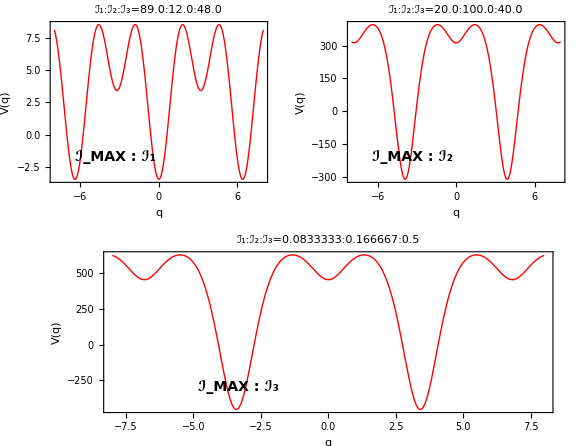

```mathematica
GraphicsGrid[{{p1[1],p1[2]}, 
 {p1[3],SpanFromLeft}},ImageSize->Large,Frame->All]
```

## Energy expression for H’

## raduta

```mathematica
HprimRaduta[spin_,theta_,fi_]:=x3[spin,theta]^2(u-Sin[fi]^2-v0/spin*Cos[theta])+spin^2 Sin[fi]^2+2*v0*spin*Cos[fi];
```

## personal

```mathematica
HprimCalc[spin_,theta_,fi_]:=x3[spin,theta]^2(u-Sin[fi]^2)+spin^2 Sin[fi]^2+2v0*spin*Sin[fi]*Cos[fi];
```

```mathematica
HprimCalc[9.5,0,0]
```

131.432

```mathematica
HprimRaduta[9.5,0,0]
```

224.887